```mathematica
Clear[x]
```

x'[t]==-1.386 x[t]

{{x[t]→1. ⅇ^(-1.386 t)}}

1. ⅇ^(-1.386 t)

{{y[t]→1.11111 ⅇ^(-1.5246 t) (-1. ⅇ^(0.1386 t)+1. ⅇ^(1.386 t))}}

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

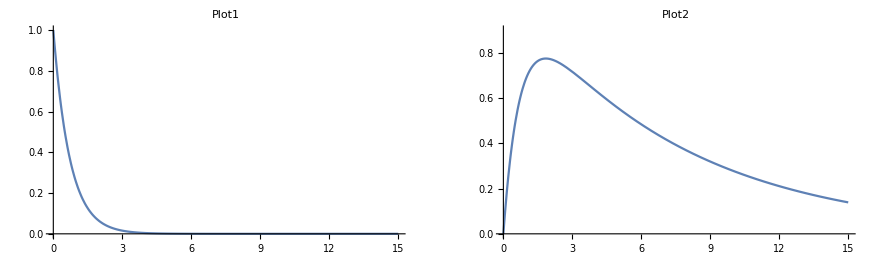

```mathematica
k1=1.386; k2=0.1386;
hours=15;
de1=x'[t]==-k1*x[t]
sol1 = DSolve[{de1,x[0]==x0},x[t],t]
x0=1;
x[t] =First[x[t]/.sol1]
de2=y'[t]==k1*x[t] - k2*y[t];
sol2 = DSolve[{de2,y[0]==y0},y[t],t]
y0 = 0;
plot1 = Plot[x[t]/.sol1,{t,0,hours},PlotRange->{0,1},PlotLabel->"Plot1"];
plot2 = Plot[y[t]/.sol2,{t,0,hours},PlotRange->{0,0.9},PlotLabel->"Plot2"];
GraphicsArray[{plot1,plot2},Frame->True]
```

Course of pill

```mathematica
Clear[x]
```

x'[t]==2-1.386 x[t]

{{x[t]→1.443 ⅇ^(-1.386 t) (-0.307+1. ⅇ^(1.386 t))}}

1.443 ⅇ^(-1.386 t) (-0.307+1. ⅇ^(1.386 t))

{{y[t]→14.43 ⅇ^(-1.386 t) (0.0341111-1.03411 ⅇ^(1.2474 t)+1. ⅇ^(1.386 t))}}

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

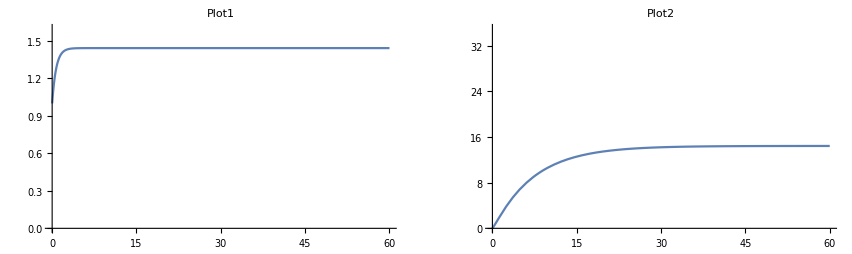

```mathematica
k1=1.386; k2=0.1386;i=2;
hours=60;
de1=x'[t]==i-k1*x[t]
sol1 = DSolve[{de1,x[0]==x0},x[t],t]
x0=1;
x[t] =First[x[t]/.sol1]
de2=y'[t]==k1*x[t] - k2*y[t];
sol2 = DSolve[{de2,y[0]==y0},y[t],t]
y0 = 0;
plot1 = Plot[x[t]/.sol1,{t,0,hours},PlotRange->{0,1.6},PlotLabel->"Plot1"];
plot2 = Plot[y[t]/.sol2,{t,0,hours},PlotRange->{0,35},PlotLabel->"Plot2"];
GraphicsArray[{plot1,plot2},Frame->True]
```